```mathematica
(* In this program, we fix d=13 and plot the b-solution Subscript[f, b] and Subscript[Psi, b] for a fixed b. We also plot the Subscript[u, ∞] and Subscript[Psi, ∞] solutions. Then, we estimate the Morse index of Subscript[M, b] and Subscript[M, ∞] by computing Subscript[M, b] γ=0 and Subscript[M, ∞] γ=0 with the Gaussian right initial condition *)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
d=13;
b=1;
rmin=10^(-10);
rmax=9;
tolmin = 0.001;
maxiter = 1000;
NL2={D[#2,r]+(d-1)/r #2-r^2 #1+#3 #1+#1^3==0,#2==D[#1,r]}&;
bound={#1[rmin]==b,#2[rmin]==0}&;

(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
tol=1;
(* Solve the b-IVP for the ground state in the loop, check the value of the solution at rmax. If the value is greater than zero, update λ using bisection and keep going. Stop when either the value of the solution is negative, or we did more iterations than maxiter *)
For[i=1,tol>tolmin,i++,
sol=NDSolve[{NL2[f1[r],f2[r],λ],bound[f1,f2]},{f1[r],f2[r]},{r,rmin,rmax}];
If[(f1[r]/.sol[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[f1[r]/.sol[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
λb = λ;
solf = sol;
```

```mathematica
(* Here, we find the corresponding Subscript[F, ∞] solution, same method for λ *)
```

```mathematica
NLF={D[#2,r]+(d-3)/r #2-(d-3)/r^2 #1-r^2#1+#3 #1+1/r^2#1^3==0,#2==D[#1,r]}&;
boundF={#1[rmin]==Sqrt[d-3],#2[rmin]==0}&;
(* λ bounds for the bisection method *)
λmin = 0;
λmax = d;
λ=(λmin+λmax)/2;
(* Loop goes until either tolerance is satisfied, or maxiter is exceeded *)
tol=1;
For[i=1,tol>tolmin,i++,
sol=NDSolve[{NLF[F1[r],F2[r],λ],boundF[F1,F2]},{F1[r],F2[r]},{r,rmin,rmax}];
If[(F1[r]/.sol[[1]][[1]]/.r->rmax)>0,{λ,λmin,λmax}={(λ+λmax)/2,λ,λmax},{λ,λmin,λmax}={(λ+λmin)/2,λmin,λ}];
tol = Abs[F1[r]/.sol[[1]][[1]]/.r->rmax];
If[i>maxiter,Break[],]];
Subscript[λ, ∞]=λ;
solF =sol;
```

```mathematica
(* Calculate Subscript[Psi, b] and Subscript[Psi, ∞] using change of variables Subscript[Psi, b](t)=e^t*Subscript[f, b](e^t), Subscript[Psi, ∞](t)= Subscript[F, ∞](e^t) *)
```

```mathematica
Psib = Exp[t]*(f1[r]/.solf/.r->Exp[t]);
Psiinf = F1[r]/.solF/.r->Exp[t];
```

```mathematica
(* Plot Subscript[f, b](r) and Subscript[F, ∞](r), and then Subscript[Psi, b](t) and Subscript[Psi, ∞](t) *)
```

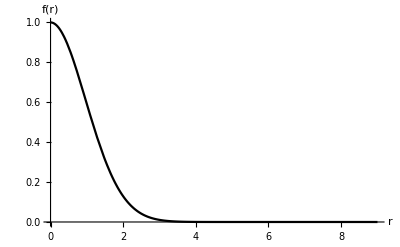

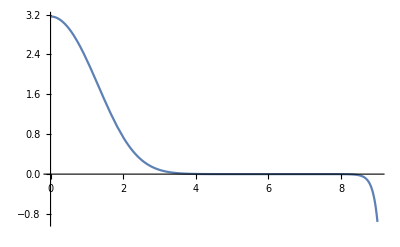

```mathematica
Plot[Evaluate[f1[r]/.solf],{r,rmin,rmax},PlotRange->All,PlotStyle->Black,AxesStyle->Directive[Black,Larger],AxesLabel->{r,f[r]}]
Plot[Evaluate[F1[r]/.solF],{r,rmin,rmax},PlotRange->All]
```

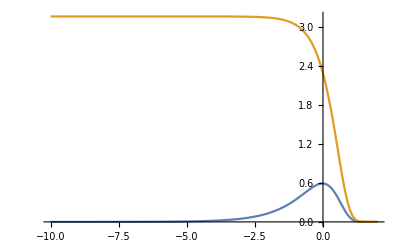

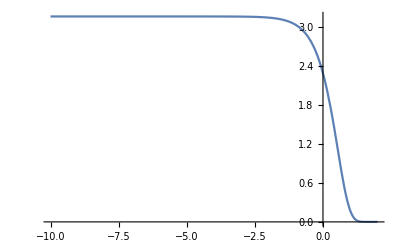

```mathematica
Plot[{Psib,Psiinf},{t,-10,2},PlotRange->All]
Plot[Psiinf,{t,-10,2},PlotRange->All]
```

```mathematica
(* Morse index estimates. We solve equations Subscript[M, b] γ=0 and Subscript[M, ∞] γ=0 with the right initial condition given by the Gaussian decay: γ(t)-> e^(-1/2 e^(2t))e^((λ-d+2)/2 t),γ'(t) -> e^(-1/2 e^(2t))e^((λ-d+2)/2 t)(-e^(2t)+(λ-d+2)/2 t) as t->-∞.  *)
```

```mathematica
tmax=Log[7];
tmin = -10;
rbc1b = Exp[-1/2 Exp[2 tmax]+tmax (λb-d+2)/2 ];
rbc2b =Exp[-1/2 Exp[2 tmax]+tmax (λb-d+2)/2 ](-Exp[2tmax]+tmax(λb-d+2)/2);
solMb = NDSolve[{gam2'[t]+(d-4)gam2[t]+(3-d)gam1[t]+3 *Psib^2*gam1[t] +λb Exp[2t]gam1[t]-Exp[4t]gam1[t]==0,gam2[t]==gam1'[t],gam1[tmax]==rbc1b,gam2[tmax]==rbc2b},{gam1[t],gam2[t]},{t,tmin,tmax}];
solMinf = NDSolve[{gam2'[t]+(d-4)gam2[t]+(3-d)gam1[t]+3 *Psiinf^2*gam1[t] +Subscript[λ, ∞] Exp[2t]gam1[t]-Exp[4t]gam1[t]==0,gam2[t]==gam1'[t],gam1[tmax]==rbc1b,gam2[tmax]==rbc2b},{gam1[t],gam2[t]},{t,tmin,tmax}];
```

-Graphics-

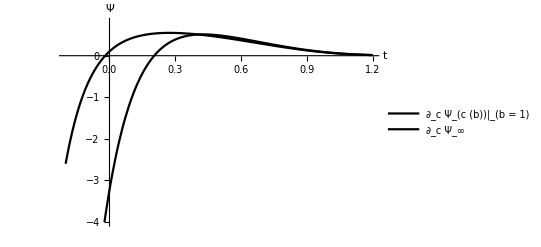

```mathematica
Plot[{Evaluate[gam1[t]/.solMb],Evaluate[gam1[t]/.solMinf]},{t,-10,1.5},PlotRange->All,PlotLegends->Placed[{"∂_c Ψ_(c (b))|_(b = 1)","∂_c Ψ_∞"},{Left,Center}],AxesLabel->{"t","Ψ"}]
Plot[{Evaluate[gam1[t]/.solMb],Evaluate[gam1[t]/.solMinf]},{t,-0.2,1.2},PlotRange->{-4,0.8},PlotLegends->Placed[{"∂_c Ψ_(c (b))|_(b = 1)","∂_c Ψ_∞"},Center],PlotStyle->Black,AxesStyle->Directive[Black,Medium],AxesLabel->{"t","Ψ"}]
```

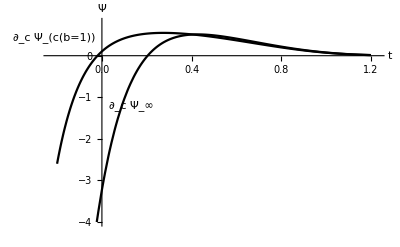

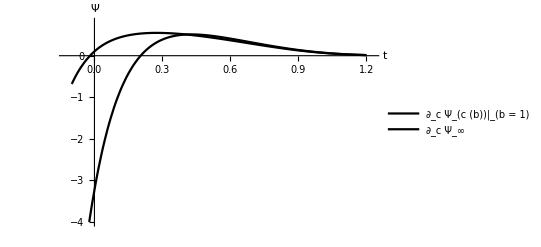

```mathematica
□(* Transform to the r-variables and plot v(r)=1/r Psi(ln(r)) *)
```

```mathematica
vb = 1/r*(gam1[t]/.solMb/.t->Log[r]);
vinf = 1/r*(gam1[t]/.solMinf/.t->Log[r]);
```

-Graphics-

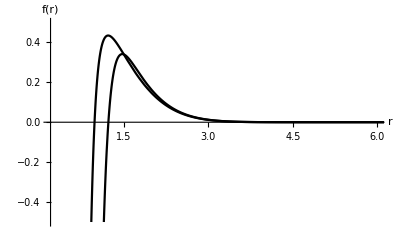

```mathematica
Plot[{vb,vinf},{r,Exp[tmin],Exp[tmax]},PlotRange->All,PlotLegends->Placed[{"∂_c Ψ_(c (b))","∂_c Ψ_∞"},{Top,Center}],AxesLabel->{r,f[r]}]
Plot[{vb,vinf},{r,Exp[tmin],Exp[tmax]},PlotRange->{{0.2,6},{-0.5,0.5}},AxesLabel->{r,f[r]},PlotStyle->Black,AxesStyle->Directive[Black,Medium]]
```

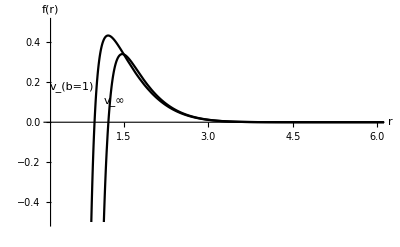

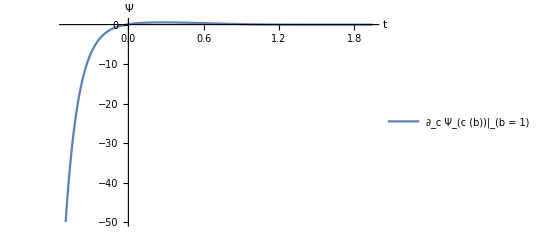

```mathematica
Plot[Evaluate[gam1[t]/.solMb],{t,-0.5,tmax},PlotRange->All,PlotLegends->Placed[{"∂_c Ψ_(c (b))|_(b = 1)","∂_c Ψ_∞"},{Left,Center}],AxesLabel->{"t","Ψ"}]
```

```mathematica
Plot[Evaluate[gam1[t]/.solMb],{t,-0.1,1.5},PlotRange->All,PlotLegends->Placed[{"∂_c Ψ_(c (b))|_(b = 1)"},Center],AxesLabel->{"t","Ψ"},PlotStyle->Thickness[0.01]]
```

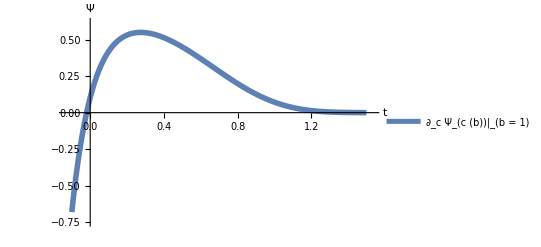

```mathematica
SubMinus[κ]=-(d-4)/2-Sqrt[d^2-16d+40]/2
```

-5

```mathematica
Plot[Evaluate[gam1[t]/.solMinf],{t,-0.1,1.5},PlotRange->All,PlotLegends->Placed[{"∂_c Ψ_∞"},Center],AxesLabel->{"t","Ψ"},PlotStyle->Thickness[0.01]]
```

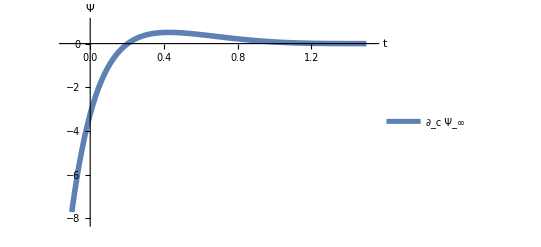

```mathematica
Plot[vb,{r,Exp[-0.1],Exp[1.5]},PlotRange->All,PlotLegends->Placed[{"r^-1∂_c Ψ_(c (b))(ln(r))|_(b = 1)"},{Top,Center}],AxesLabel->{"r","f(r)"},PlotStyle->Thickness[0.01]]
```

```mathematica
Plot[vinf,{r,Exp[-0.1],Exp[1.5]},PlotRange->All,PlotLegends->Placed[{"r^-1∂_c Ψ_∞(ln(r))"},{Top,Center}],AxesLabel->{"r","f(r)"},PlotStyle->Thickness[0.01]]
```

-Graphics-

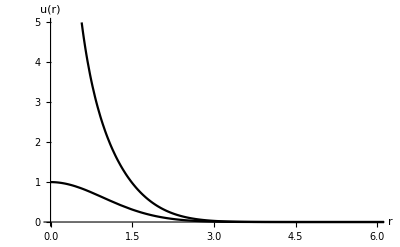

```mathematica
Plot[Evaluate[f1[r]/.solf],{r,rmin,rmax},PlotRange->All,PlotStyle->Black,AxesStyle->Directive[Black,Larger],AxesLabel->{r,f[r]}]
Plot[{Evaluate[f1[r]/.solf],Evaluate[F1[r]/r/.solF]},{r,rmin,rmax},PlotRange->{{0,6},{0,5}},PlotStyle->Black,AxesStyle->Directive[Black,Larger],AxesLabel->{r,u[r]}]
```

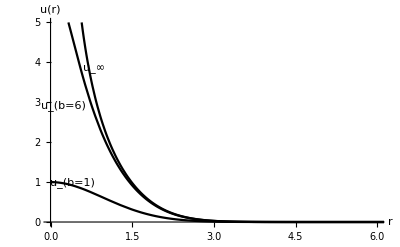

```mathematica
Plot[{Psib,Psiinf},{t,-10,2},PlotRange->All,PlotStyle->Black,AxesStyle->Directive[Black,Larger],AxesLabel->{t,Ψ[t]}]
```

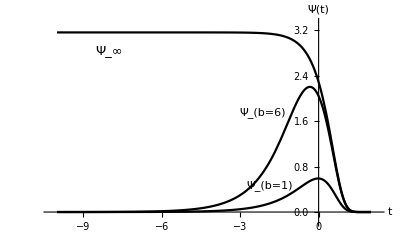

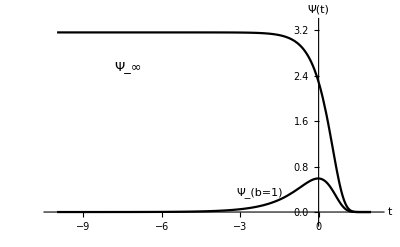

```mathematica
CurrentValue[EvaluationNotebook[],InputAliases]={"at"->SubscriptBox[RowBox[{"■",StyleBox["|",FontFamily->"Times"]}],"□"]}
```